3.30416

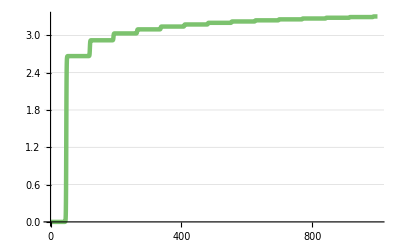

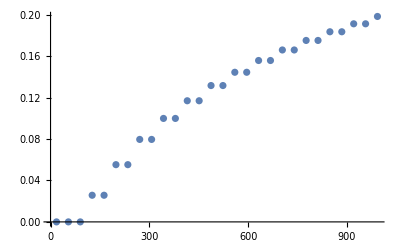

```mathematica
Get[NotebookDirectory[]<>"pi.m"];
rsys=PiRsys[];
tmax=1000;
sol=SimulateRxnsys[ExpandRsys[rsys], tmax];
EvaluateRxnAtPoint[sol,pi,tmax]
PlotForPaper[Evaluate[{pi[t]}/.sol], tmax, 200]
errorMap=EvaluateError[rsys, tmax];
piErrorList=errorMap[pi]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[piErrorList,Ticks->{Range[0,tmax,100],Automatic}]
```